```mathematica
SetDirectory["~/iCloud/Projects/2022/MachineLearning/Data/"]
```

/Users/adrianbaule/Library/Mobile Documents/com~apple~CloudDocs/Projects/2022/MachineLearning/Data

```mathematica
testshapes=Import["Densities_of_testshapes.csv"];
```

```mathematica
testshapes//MatrixForm
```

( | molecule_name | molecule_volume | n_spheres | Roth_densities | Voronoi_mean | Voronoi_error | Centroid_mean | Centroid_error
0 | molecule2805 | 8.06039 | 5 | 0.730004 | 0.731046 | 0.00120751 | 0.730679 | 0.00110408
1 | molecule149 | 8.236 | 4 | 0.691799 | 0.693624 | 0.00150798 | 0.695391 | 0.00220684
2 | molecule458 | 9.483 | 4 | 0.715093 | 0.712613 | 0.000881605 | 0.712724 | 0.00114247
3 | molecule476 | 9.3973 | 5 | 0.676831 | 0.676228 | 0.00112977 | 0.677633 | 0.00133911
4 | molecule481 | 8.62642 | 4 | 0.727237 | 0.726732 | 0.00101794 | 0.726231 | 0.0011444)

```mathematica
rank={5,3,4,6,2}
```

{5,3,4,6,2}

```mathematica
tsrj=Table[{i,testshapes[[rank[[i]],5]]},{i,1,5}]
tsvoronoi=Table[{i,Around[testshapes[[rank[[i]],6]],√10 testshapes[[rank[[i]],7]]]},{i,1,5}]
tsvoronoi2=Table[{i,testshapes[[rank[[i]],6]]},{i,1,5}]
tscentroid=Table[{i,Around[testshapes[[rank[[i]],8]],√10 testshapes[[rank[[i]],9]]]},{i,1,5}]
tscentroid2=Table[{i,testshapes[[rank[[i]],8]]},{i,1,5}]
```

{{1,0.676831},{2,0.691799},{3,0.715093},{4,0.727237},{5,0.730004}}

{{1,0.6760.004},{2,0.6940.005},{3,0.71260.0028},{4,0.72670.0032},{5,0.7310.004}}

{{1,0.676228},{2,0.693624},{3,0.712613},{4,0.726732},{5,0.731046}}

{{1,0.6780.004},{2,0.6950.007},{3,0.7130.004},{4,0.7260.004},{5,0.73070.0035}}

{{1,0.677633},{2,0.695391},{3,0.712724},{4,0.726231},{5,0.730679}}

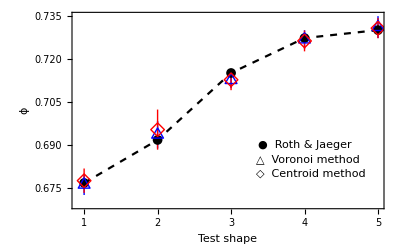

```mathematica
Show[ListPlot[{tsrj,tsvoronoi,tscentroid},PlotMarkers->{{"●",10},{"△",14},{"◇",14}},PlotStyle->{{Black,Dashed},Blue,Red},Joined->{True,False,False}],Frame->True,Axes->False,FrameStyle->Black,FrameTicks->{{1,2,3,4,5},Automatic,None,None},FrameLabel->{"Test shape","ϕ"},LabelStyle->12,Epilog->{Inset[Style["●",Black,12]Style[" Roth & Jaeger",12,FontFamily->"Helvetica"],{4,0.69}],Inset[Style["△",Blue,14]Style[" Voronoi method",12,FontFamily->"Helvetica"],{4.05,0.685}],Inset[Style["◇",Red,14]Style[" Centroid method",12,FontFamily->"Helvetica"],{4.08,0.68}]}]
```

```mathematica
pathshapes=Import["Density_of_shapesforPC1=-4.csv"];
```

```mathematica
pathshapes//MatrixForm
```

( | molecule_name | molecule_volume | n_spheres | Voronoi_mean | Voronoi_error | Centroid_mean | Centroid_error
0 | molecule1 | 7.40306 | 5 | 0.715301 | 0.00122286 | 0.717855 | 0.000860897
1 | molecule2 | 5.52597 | 4 | 0.72004 | 0.000584413 | 0.72115 | 0.000592443
2 | molecule3 | 4.66033 | 3 | 0.700016 | 0.000684514 | 0.70081 | 0.000610994
3 | molecule4 | 5.4061 | 5 | 0.722232 | 0.00120652 | 0.723775 | 0.00144462
4 | molecule5 | 8.27166 | 5 | 0.717405 | 0.000655012 | 0.719767 | 0.000738444
5 | molecule6 | 10.6487 | 5 | 0.691856 | 0.00104349 | 0.692994 | 0.00220211)

```mathematica
yvals={-10,-4.1135,0.3191,3.2168,10,16}
psvoronoi=Table[{-yvals[[i-1]],Around[pathshapes[[i,5]],√10 pathshapes[[i,6]]]},{i,2,6}]
pscentroid=Table[{-yvals[[i-1]],Around[pathshapes[[i,7]],√10 pathshapes[[i,8]]]},{i,2,6}]
```

{-10,-4.1135,0.3191,3.2168,10,16}

{{10,0.7150.004},{4.1135,0.72000.0018},{-0.3191,0.70000.0022},{-3.2168,0.7220.004},{-10,0.71740.0021}}

{{10,0.71790.0027},{4.1135,0.72120.0019},{-0.3191,0.70080.0019},{-3.2168,0.7240.005},{-10,0.71980.0023}}

```mathematica
pp=Import["pathpoints2.csv"];
```

```mathematica
pp2=Table[{-pp[[i,1]],pp[[i,2]]},{i,1,Length[pp]}];
```

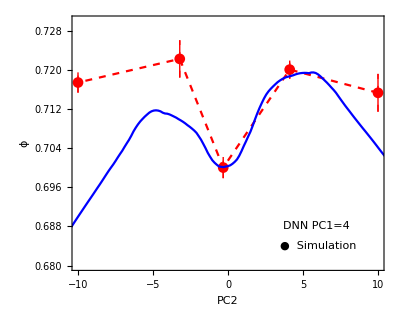

```mathematica
Show[ListPlot[{psvoronoi},PlotStyle->Red,PlotMarkers->{"●",11},Joined->False],
ListPlot[psvoronoi,PlotStyle->{Red,Dashed},PlotMarkers->None,Joined->True],
ListPlot[{pp2},PlotStyle->{Blue},Joined->{True}],PlotRange->{{-10,10},{0.68,0.73}},Frame->True,Axes->False,FrameLabel->{"PC2","ϕ"},FrameStyle->Black,FrameTicks->{Automatic,Automatic,None,None},LabelStyle->12,AspectRatio->0.8,Epilog->{Inset[Style["●",Red,12]Style[" Simulation",12,FontFamily->"Helvetica"],{6,0.684}],Inset[Graphics[{Blue,Thick,Line[{{-0.4,0},{0,0}}]}]Style[" DNN PC1=4",12,FontFamily->"Helvetica"],{5.9,0.688}]}]
```

```mathematica
pd=Import["Densities_of_densest_shapes.csv"];
```

```mathematica
pd//MatrixForm
```

( | molecule_name | molecule_volume | n_spheres | Voronoi_mean | Voronoi_error | Centroid_mean | Centroid_error
0 | maxPC2 | 7.95828 | 5 | 0.731823 | 0.00113796 | 0.731262 | 0.00145571
1 | maxPC3 | 8.04618 | 5 | 0.731778 | 0.00127579 | 0.731895 | 0.00125988
2 | maxPC4 | 8.06963 | 5 | 0.732806 | 0.000831021 | 0.732576 | 0.00119575
3 | maxPC5 | 8.34174 | 5 | 0.732757 | 0.000693132 | 0.732551 | 0.000968163
4 | maxPC6 | 8.30929 | 5 | 0.731508 | 0.00120748 | 0.731462 | 0.00161412)

```mathematica
pdcentroid=Table[{i,pd[[i,7]]},{i,2,6}]
pdcentroid2=Table[{i,Around[pd[[i,7]],√10 pd[[i,8]]]},{i,2,6}]
pdvoronoi2=Table[{i,Around[pd[[i,5]],√10 pd[[i,6]]]},{i,2,6}]
```

{{2,0.731262},{3,0.731895},{4,0.732576},{5,0.732551},{6,0.731462}}

{{2,0.7310.005},{3,0.7320.004},{4,0.7330.004},{5,0.73260.0031},{6,0.7310.005}}

{{2,0.7320.004},{3,0.7320.004},{4,0.73280.0026},{5,0.73280.0022},{6,0.7320.004}}

```mathematica
pdprediction={{2,0.734},{3,0.734},{4,0.734},{5,0.734},{6,0.734}}
```

{{2,0.734},{3,0.734},{4,0.734},{5,0.734},{6,0.734}}

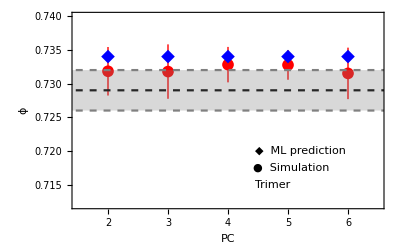

```mathematica
Show[ListPlot[pdvoronoi2,PlotMarkers->{"●",12},PlotStyle->Red],
ListPlot[pdprediction,PlotMarkers->{"◆",14},PlotStyle->Blue],
Plot[{0.729,0.726},{x,1,6.8},PlotStyle->{{Black,Dashed},{Gray,Dashed}}],Plot[0.732,{x,1,6.8},PlotStyle->{Gray,Dashed},Filling->0.726,FillingStyle->{Gray,Opacity[0.3]}],PlotRange->{{1.5,6.5},{0.712,0.74}},Frame->True,Axes->False,FrameStyle->Black,FrameTicks->{{2,3,4,5,6},Automatic,None,None},FrameLabel->{"PC","ϕ"},LabelStyle->12,Epilog->{Inset[Style["◆",Blue,14]Style[" ML prediction",12,FontFamily->"Helvetica"],{5.2,0.72}],Inset[Style["●",Red,12]Style[" Simulation",12,FontFamily->"Helvetica"],{5.05,0.7175}],Inset[Graphics[{Black,Dashed,Thick,Line[{{-0.4,0},{0,0}}]}]Style[" Trimer",12,FontFamily->"Helvetica"],{4.75,0.715}]}]
```

```mathematica
data=Import["5sphere_20dim.csv"]
```

{{0.726481,0,0,0,0.349044,0.265928,0.972677,0.349044,5,0,0,0,2.,1.56185,2.,2.,2.},5799}
 |  |  |  |

```mathematica
phi=Table[data[[i,1]],{i,1,Length[data]}];
alpha=Table[Rest[data[[i]]],{i,1,Length[data]}];
```

```mathematica
pcared2=DimensionReduction[alpha,2,Method->"PrincipalComponentsAnalysis"]
```

DimensionReducerFunction[…]

```mathematica
alpha2=pcared2[alpha]
```

{{-3.61181,0.310406},{-0.406577,3.56938},5797,{0.848901,-0.107694}}
 |  |  |  |

```mathematica
alphaset=Table[{alpha2[[i,1]],alpha2[[i,2]]},{i,1,Length[phi]}]
```

{{-3.61181,0.310406},{-0.406577,3.56938},5797,{0.848901,-0.107694}}
 |  |  |  |

```mathematica
testshapes//MatrixForm
```

( | molecule_name | molecule_volume | n_spheres | Roth_densities | Voronoi_mean | Voronoi_error | Centroid_mean | Centroid_error
0 | molecule2805 | 8.06039 | 5 | 0.730004 | 0.731046 | 0.00120751 | 0.730679 | 0.00110408
1 | molecule149 | 8.236 | 4 | 0.691799 | 0.693624 | 0.00150798 | 0.695391 | 0.00220684
2 | molecule458 | 9.483 | 4 | 0.715093 | 0.712613 | 0.000881605 | 0.712724 | 0.00114247
3 | molecule476 | 9.3973 | 5 | 0.676831 | 0.676228 | 0.00112977 | 0.677633 | 0.00133911
4 | molecule481 | 8.62642 | 4 | 0.727237 | 0.726732 | 0.00101794 | 0.726231 | 0.0011444)

```mathematica
pc2values={{{0.9406684758473851,0.41498053315859973}},{{0.8518101959746452,0.4100304369014315}},{{0.7147374771948363,0.3643586901682109}},{{0.8419025859124644,0.2036942437469097}},{{0.6851645560625329,0.10028825608742836}}}
```

{{{0.940668,0.414981}},{{0.85181,0.41003}},{{0.714737,0.364359}},{{0.841903,0.203694}},{{0.685165,0.100288}}}

```mathematica
alphaset2=Table[{-alphaset[[i,1]],-alphaset[[i,2]]},{i,1,Length[alphaset]}]
pc2values2=Table[{{-pc2values[[i,1,1]],-pc2values[[i,1,2]]}},{i,1,5}]
```

{{3.61181,-0.310406},{0.406577,-3.56938},5797,{-0.848901,0.107694}}
 |  |  |  |

{{{-0.940668,-0.414981}},{{-0.85181,-0.41003}},{{-0.714737,-0.364359}},{{-0.841903,-0.203694}},{{-0.685165,-0.100288}}}

```mathematica
dense={};
Do[If[phi[[i]]>0.73,Block[{},AppendTo[dense,i]]],{i,1,Length[phi]}]
```

```mathematica
Length[dense]
```

1116

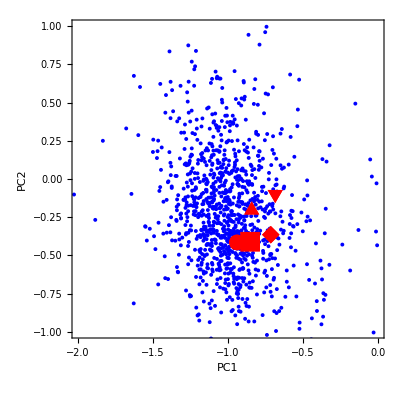

```mathematica
Show[ListPlot[alphaset2[[dense]],PlotMarkers->{"●",4},PlotStyle->Blue],ListPlot[pc2values2,PlotMarkers->{{"●",16},{"■",20},{"◆",18},{"▲",18},{"▼",18}},PlotStyle->Red],PlotRange->{{-2,0},{-1,1}},Frame->True,FrameLabel->{"PC1","PC2"},FrameStyle->Black,Axes->None,AspectRatio->1]
```

```mathematica
a=0.45;
ss={0,0,0,0,0,0,a,0,0,-Sin[π/6]a,Cos[π/6]a,0,-Sin[π/6]a,-Cos[π/6]a,0,1.,1.,2.,2.,2.}
Graphics3D[{Red,Sphere[{ss[[1]],ss[[2]],ss[[3]]},0.5ss[[16]]],Red,Sphere[{ss[[4]],ss[[5]],ss[[6]]},0.5ss[[17]]],Red,Sphere[{ss[[7]],ss[[8]],ss[[9]]},0.5ss[[18]]],Red,Sphere[{ss[[10]],ss[[11]],ss[[12]]},0.5ss[[19]]],Red,Sphere[{ss[[13]],ss[[14]],ss[[15]]},0.5ss[[20]]]},Boxed->False]
```

{0,0,0,0,0,0,0.45,0,0,-0.225,0.389711,0,-0.225,-0.389711,0,1.,1.,2.,2.,2.}

-Graphics3D-

```mathematica
ss=pcared2[{-5,10},"OriginalVectors"]
Graphics3D[{Red,Sphere[{ss[[1]],ss[[2]],ss[[3]]},0.5ss[[16]]],Red,Sphere[{ss[[4]],ss[[5]],ss[[6]]},0.5ss[[17]]],Red,Sphere[{ss[[7]],ss[[8]],ss[[9]]},0.5ss[[18]]],Red,Sphere[{ss[[10]],ss[[11]],ss[[12]]},0.5ss[[19]]],Red,Sphere[{ss[[13]],ss[[14]],ss[[15]]},0.5ss[[20]]]},Boxed->False]
```

{0.,0.,0.,0.261242,-0.67331,1.08736,0.48785,-0.983011,1.01912,0.569021,-1.06485,0.799149,0.188165,-0.668903,0.372471,2.,1.46927,1.55548,1.79257,1.88213}

-Graphics3D-

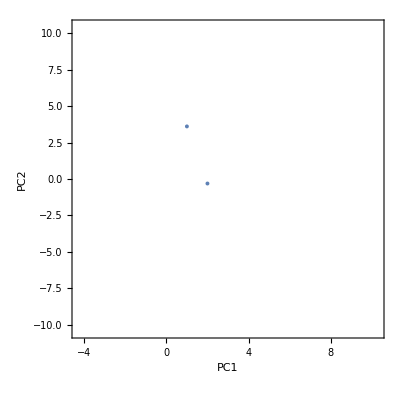

```mathematica
ListPlot[alphaset2[[1]],PlotMarkers->{"●",4},PlotRange->{{-4.3,10.3},{-10.5,10.5}},Frame->True,FrameLabel->{"PC1","PC2"},FrameStyle->Black,Axes->None,AspectRatio->1]
```